```mathematica
SetDirectory["C:\Program Files\Daedalon"]
```

SetDirectory::cdir: Cannot set current directory to C:\Program Files\Daedalon.

$Failed

```mathematica
SetDirectory["C:\Seth\courses\physics39\phys39_fall06\web-content\chaos"]
```

C:\Seth\courses\physics39\phys39_fall06\web-content\chaos

Set the directory to where a data file from the Daedalon Pendulum is stored.

```mathematica
myList=Import["test.pha","Table"];
```

The first two values aren't interesting and can be discarded. The rest of the data comes in groups of four, time, angle, velocity and something else.

```mathematica
Shallow[InputForm[myList]]
```

{{<<1>>}, {<<1>>}, {<<4>>}, {<<4>>}, {<<4>>}, {<<4>>}, {<<4>>}, {<<4>>}, {<<4>>}, {<<4>>}, <<9993>>}

```mathematica
Take[myList,6]
```

{{10000},{PHASE},{0.0193,2.6154,-19.8901,0},{0.0212,2.6154,-14.2426,0},{0.0232,2.6154,-1.8509,0},{0.0253,2.6138,-0.1674,0}}

```mathematica
myList[[3]]
```

{0.0193,2.6154,-19.8901,0}

```mathematica
myList[[10000]]
```

{20.0234,2.6735,-1.5682,0}

The first two values are junk, another element is the entire list, then that leaves a 9998 long list with each element containing 4 elements.

```mathematica
Dimensions[myList]
```

{10003}

```mathematica
Array[phaseplot,{9998,2}];
```

```mathematica
For[i=1,i≤9998,i++,
    phaseplot[i,1]=myList[[i+2]][[1]];
 phaseplot[i,2]=myList[[i+2]][[2]];  
]
```

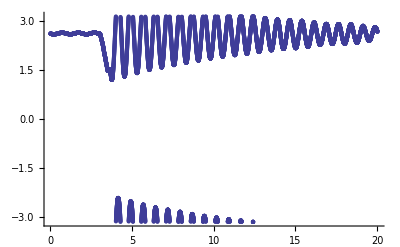

```mathematica
ListPlot[Array[phaseplot,{9998,2}],PlotRange->All]
```

```mathematica
For[i=1,i≤9998,i++,
 If[ phaseplot[i,2]<0,phaseplot[i,2]=phaseplot[i,2]+2π,phaseplot[i,2]=phaseplot[i,2] ]
]
```

Fix the data modulo 2π.

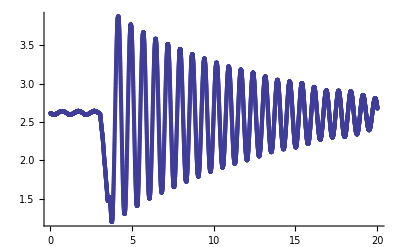

```mathematica
ListPlot[Array[phaseplot,{9998,2}],PlotRange->All]
```

Make an array 9998 rows long with each row containing 2 entries. Take the last 7000 entries and discard the rest.

```mathematica
data=Array[phaseplot,{9998,2}];
```

```mathematica
data1=Take[data,-7000];
```

Plot the data.

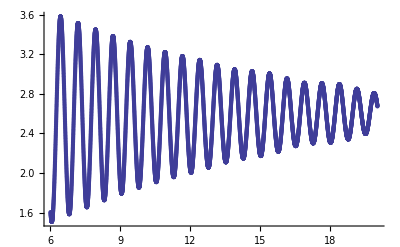

```mathematica
ListPlot[data1,PlotRange->All]
```

FIt the data to a damped cosine.

```mathematica
model= Amp *Exp[-a* t]*Cos[√(ω^2-a^2)t  + θ]+Base
```

Base+Amp ⅇ^(-a t) Cos[θ+t √(-a^2+ω^2)]

```mathematica
fitted =FindFit[data1,model,{{Amp,1},{Base,2.7}, {ω,6.2},{θ,2.5},{a,.1}},t]
```

{Amp→-2.07995,Base→2.5788,ω→8.42562,θ→-13.5156,a→0.108648}

```mathematica
fit =model/.fitted
```

2.5788-2.07995 ⅇ^(-0.108648 t) Cos[13.5156-8.42492 t]

Make an array of the fitted values.

```mathematica
f1 =Table[fit,{t,0,20,.02}];
```

```mathematica
Take[f1,6]
```

{1.36768,1.10446,0.88406,0.712519,0.594478,0.533042}

Make a 2D array of the time and  fitted values.

```mathematica
data2=Table[{t,fit},{t,0,20,.01}];
```

```mathematica
Take[data2,6]
```

{{0.,1.36768},{0.01,1.23115},{0.02,1.10446},{0.03,0.9885},{0.04,0.88406},{0.05,0.791857}}

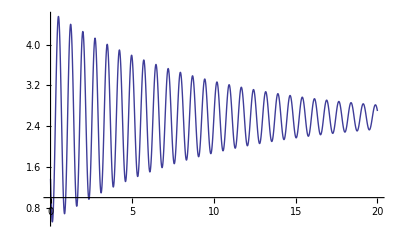

```mathematica
Plot[fit,{t,0,20}]
```

```mathematica
ListPlot[data1,PlotRange->All]
```

-Graphics-

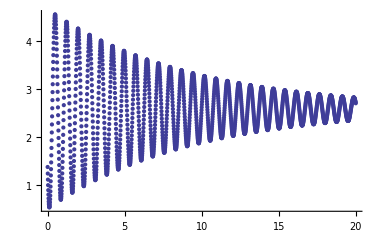

```mathematica
ListPlot[data2,PlotRange->All]
```

Compare data with fitted data.

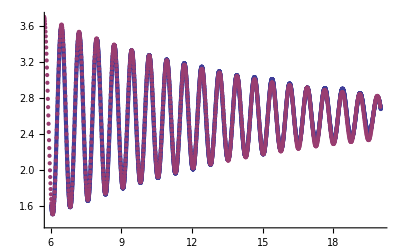

```mathematica
ListPlot[{data1,data2},PlotRange->{{6,20},{1.4,3.7}}]
```

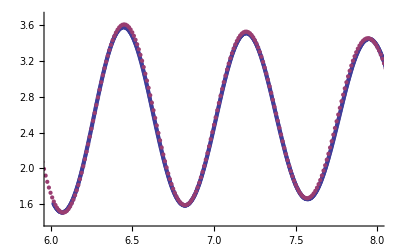

```mathematica
ListPlot[{data1,data2},PlotRange->{{6,8},{1.4,3.7}}]
```